# Analytical calculations for M = 1 (large N limit)

```mathematica
ClearAll["Global`*"]
```

```mathematica
πgeneral[i_]:= -(Subscript[s, {i,a}])(b-c) + 1/2 ∑_(l=1)^n ExpandAll[(-c (Subscript[s, {i,a}]+Subscript[s, {i,d}])+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, i] Subscript[h, l](Subscript[s, {i,a}]-Subscript[s, {i,d}])+b Subscript[h, i] Subscript[h, l] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
πstrat[i_,sia_,sid_]:= (*sia,sid∈{0,1} to indicate strategy*)-(sia)(b-c) + 1/2 ∑_(l=1)^n ExpandAll[(-c (sia+sid)+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, i] Subscript[h, l](sia-sid)+b Subscript[h, i] Subscript[h, l] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
```

```mathematica
πCC[i_]:=πstrat[i,1,1]
πCD[i_]:=πstrat[i,1,0] 
πDC[i_]:=πstrat[i,0,1]
πDD[i_]:=πstrat[i,0,0]
```

The strategy-specific payoffs are therefore

```mathematica
πCC[i]
πCD[i]
πDC[i]
πDD[i]
```

-b+c+1/2 ∑_(l=1)^n (-2 c+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

-b+c+1/2 ∑_(l=1)^n (-c-c h_i h_l+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

1/2 ∑_(l=1)^n (-c+c h_i h_l+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

1/2 ∑_(l=1)^n (b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

Compare two ways of computing the total sum

```mathematica
(*under neutrality, we assume that the population is divided equally into the four strategies*)
total1=n/4(πCC[i]+πCD[i]+πDC[i]+πDD[i])//.unbracketRule//FullSimplify;
(*under neutrality, we assume that the population is divided equally into the four strategies*)
total2=∑_(j=1)^n πgeneral[j]//.unbracketRule//FullSimplify;
```

```mathematica
(*compute difference and simplify*)
total2-total1
ExpandAll[total2-total1 ]/.{Subscript[s, {l,d}]-> Subscript[s, {l,a}],Subscript[s, {j,d}]-> Subscript[s, {j,a}]}/.{Subscript[s, {j,a}]-> 1/2}
```

-1/8 n (-4 b+4 c+n (b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})+n (-2 c+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})+n (-c-c h_i h_l+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})+n (-c+c h_i h_l+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d}))+n (-(b-c) s_{j,a}+1/2 n (-c s_{j,a}-c h_j h_l s_{j,a}-c s_{j,d}+c h_j h_l s_{j,d}+b s_{l,a}+b h_j h_l s_{l,a}+b s_{l,d}-b h_j h_l s_{l,d}))

0

```mathematica
(*use the second approach for the total payoff*)
Z[πstrat_,i_,n_]:=πstrat[i]-1/n∑_(j=1)^n πgeneral[j]//ExpandAll
```

### Defining rules

Next, we define some rules to simplify the summations:

```mathematica
(*rules for initial simplification*)
sumRule=Sum[expr1_,iter_]+Sum[expr2_,iter_]:>Sum[expr1+expr2,iter];
prodRule=Sum[expr1_,iter1_]*Sum[expr2_,iter2_]:>Sum[expr1*expr2,iter1,iter2];
revSumRule=Sum[expr1_+expr2_,iter_]:> Sum[expr1,iter]+Sum[expr2,iter];
constRule=Sum[c_?NumericQ  expr_,iter_]:>c Sum[expr,iter];
distRule=a_(b_+c_):>a*b+a*c;
dist2Rule=s_Subscript(b_+c_):>s*b+s*c;

miscRule=s_Subscript Sum[expr_,iter_]:> Sum[s*expr,iter];
squareRule = s_Subscript^2:>s;
unbracketRule=Sum[expr_,{i_,1,n}]:> n expr;

(*rules for collecting terms*)
mergeRule=a_ s1_Subscript s2_Subscript+b_ s1_Subscript s2_Subscript:> (FullSimplify[a+b])s1 s2;
```

### Simplifying expressions

```mathematica
expandBracket[bracket_]:=ExpandAll[bracket]/.revSumRule/.constRule/.distRule//.miscRule//.distRule //.squareRule//.sumRule//.unbracketRule
```

```mathematica
xCCbracket:=expandBracket[Subscript[s, {i,a}] Subscript[s, {i,d}] Z[πCC,i,n]] // FullSimplify//ExpandAll
xCDbracket:=expandBracket[Subscript[s, {i,a}](1-Subscript[s, {i,d}])Z[πCD,i,n]] //FullSimplify//ExpandAll
xDCbracket:=expandBracket[(1-Subscript[s, {i,a}])Subscript[s, {i,d}] Z[πDC,i,n]]// FullSimplify//ExpandAll
xDDbracket:=expandBracket[(1-Subscript[s, {i,a}])(1-Subscript[s, {i,d}])Z[πDD,i,n]]  // FullSimplify//ExpandAll
```

```mathematica
(*xCCbracket*)
(*xCDbracket*)
(*xDCbracket*)
(*xDDbracket*)
```

#### Simplifying the CC term

First, we define rules for relabeling quantities that are equivalent (note that the order of substitution matters here).

```mathematica
subCC1={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCC4={};
subCC2={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}] };
subCC3={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y)}; (*see the SI for definitions of y, z, g, h*)
subCC4={Subscript[s, {i,a}] Subscript[s, {i,d}] -> 1/4};
```

Then we can simplify the expression for CC as:

```mathematica
xCCbracket2=xCCbracket//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 //FullSimplify
```

((b+c (-1+n)) (-1+n) (-1+y))/(4 n)

In the limit n→∞, we can further simplify this expression:

```mathematica
xCCbracket3=FullSimplify[xCCbracket//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 ]/.{n-1->n}/.{b+c n->c n}
```

1/4 c n (-1+y)

#### Simplifying the CD term

```mathematica
subCD5={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCD6={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		(*Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],*)(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subCD7={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subCD8={Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y)};
subCD9={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,a}]->1/2};
```

```mathematica
xCDbracket2=FullSimplify[xCDbracket]//.distRule//.subCD5//.subCD6//.subCD7//.subCD8//.subCD9//FullSimplify
```

((-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z)))/(4 n)

```mathematica
(*infinit population limit*)
xCDbracket3=FullSimplify[xCDbracket//.distRule//.subCD5//.subCD6//.subCD7//.subCD8//.subCD9]/.{n-1->n,n-2->n}/.{g_-g_ n+h_ n+z_->-g n+h n}//FullSimplify
```

1/4 n (b (g-h)+c (h-z))

#### Simplifying the DC term

```mathematica
subDC10={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]}; (*same as subCD5*)
subDC11={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],(*duplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subDC12={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subDC13={Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y)};
subDC14={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,d}]->1/2};
```

```mathematica
(*simplify*)
xDCbracket2=FullSimplify[xDCbracket]//.distRule//.subDC10//.subDC11//.subDC12//.subDC13//.subDC14//FullSimplify
```

-((-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z)))/(4 n)

```mathematica
(*infinit population limit*)xDCbracket3=FullSimplify[xDCbracket//.distRule//.subDC10//.subDC11//.subDC12//.subDC13//.subDC14]/.{n-1->n,n-2->n}/.{g_-g_ n+h_ n+z_->-g n+h n}//FullSimplify
```

1/4 n (b (-g+h)+c (-h+z))

#### Simplifying the DD term

```mathematica
(*we combine the simplifications from CD and DC*)
subDD15={Subscript[h, j] Subscript[h, l] Subscript[s, {j,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {j,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y),Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y),
		Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4};
subDD16={Subscript[s, {j,a}]->1/2,Subscript[s, {j,d}]->1/2};
```

```mathematica
(*simplify*)
xDDbracket2=FullSimplify[xDDbracket]//.distRule//.subCD5//.subCD6//.subDC11//.subCD7//.subDD15//.subDD16//FullSimplify
```

-((b+c (-1+n)) (-1+n) (-1+y))/(4 n)

```mathematica
(*infinit population limit*)
xDDbracket3=FullSimplify[xDDbracket//.distRule//.subCD5//.subCD6//.subDC11//.subCD7//.subDD15//.subDD16]/.{n-1->n,n-2->n}/.{b+c n->c n}//FullSimplify
```

-1/4 c n (-1+y)

### Summary

In the infinite population limit, we have the following expressions for <∑_i α_i(π_i-1/N∑_j π_j)>:

```mathematica
Print["Z_i^CC = ",xCCbracket3,",  Z_i^CD = ",xCDbracket3,",  Z_i^DC = ",xDCbracket3,",  Z_i^DD = ",xDDbracket3]
```

Z_i^CC = 1/4 c n (-1+y),  Z_i^CD = 1/4 n (b (g-h)+c (h-z)),  Z_i^DC = 1/4 n (b (-g+h)+c (-h+z)),  Z_i^DD = -1/4 c n (-1+y)

## 2. Computing y, z, g, h in the continuous time limit

To simplify the above expressions, we need to compute the quantities y, z, g, and h as defined in the SI.

### Define functions related to coalescence time

```mathematica
γ[n_,p_]:=1-(n*p)/(2(n-1))
tt[τ_,n_,p_]:=τ*(n^2/(2γ[n,p]))
ρ[τ_,p_]:=Exp[-τ]
ρ2[τ3_,τ2_]:=3*Exp[-3*τ3]Exp[-τ2]
```

### Compute y

```mathematica
yt[t_,n_,p_,u_]:=1/2(1+(1-u/n γ[n,p])^(2*t)) (*from the SI*)
```

We then take the limit after replacing t=τ*(n^2/(2(1-p/2))) and u = μ / n:

```mathematica
ytau[μ_,τ_,p_]:=Limit[yt[tt[τ,n,p],n,p,μ/n],n->Infinity]
y[μ_,p_]:=Integrate[ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
Print["Check: ",yt[tt[τ,n,p],n,p,μ/n]//FullSimplify," ---> ",ytau[μ,τ,p]]
```

Check: 1/2 (1+(1-((1+(n p)/(2-2 n)) μ)/n^2)^(-(2 (-1+n) n^2 τ)/(2+n (-2+p)))) ---> 1/2 (1+ⅇ^(-μ τ))

We will also define a function to compute the integrals more quickly :

```mathematica
yeval[μ_,ν_]=y[μ,p];
ycalc[n_,u_,v_]=y[μ,p]/.{μ->n*u};
```

```mathematica
Print[yeval[μ,ν]," or ",ycalc[n,u,v]]
```

(2+μ)/(2+2 μ) or (2+n u)/(2+2 n u)

### Compute z

```mathematica
zt[t_,n_,p_,v_]:=(1-v/n γ[n,p])^(2*t)
```

We then take the limit after replacing t=τ*(n^2/(2γ))and v=ν/n

```mathematica
ztau[ν_,τ_,p_]:=Limit[zt[tt[τ,n,p],n,p,ν/n],n->Infinity]
z[ν_,p_]:=Integrate[ztau[ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
zeval[μ_,ν_]=z[ν,p]// FullSimplify;
zcalc[n_,u_,v_]=z[ν,p]/.{ν->n*v} // FullSimplify;
```

```mathematica
Print["Check: ",zt[tt[τ,n,p],n,p,ν/n]//FullSimplify," ---> ",ztau[ν,τ,p]]
Print[zeval[μ,ν]," or ",zcalc[n,u,v]]
```

Check: (1-((1+(n p)/(2-2 n)) ν)/n^2)^(-(2 (-1+n) n^2 τ)/(2+n (-2+p))) ---> ⅇ^(-ν τ)

1/(1+ν) or 1/(1+n v)

### Compute g

```mathematica
gtau[μ_,ν_,τ_,p_]:=ytau[μ,τ,p]*ztau[ν,τ,p]
g[μ_,ν_,p_]:=Integrate[gtau[μ,ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
geval[μ_,ν_]=g[μ,ν,p] // FullSimplify;
gcalc[n_,u_,v_]=g[μ,ν,p]/.{ν->n*v,μ->n*u}// FullSimplify;
```

```mathematica
Print["Check: ",gtau[μ,ν,τ,p]]
Print[geval[μ,ν]," or ",gcalc[n,u,v]]
```

Check: 1/2 ⅇ^(-ν τ) (1+ⅇ^(-μ τ))

1/2 (1/(1+ν)+1/(1+μ+ν)) or 1/2 (1/(1+n v)+1/(1+n (u+v)))

### Compute h

```mathematica
htau[μ_,ν_,τ3_,τ2_,p_]:=1/3(ytau[μ,τ3,p]*ztau[ν,τ3+τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3+τ2,p])
h[μ_,ν_,p_]:=Integrate[htau[μ,ν,τ3,τ2,p]*ρ2[τ3,τ2], {τ2,0,Infinity},{τ3,0,Infinity}][[1]]
heval[μ_,ν_]=h[μ,ν,p] // FullSimplify//Apart;
hcalc[n_,u_,v_]=h[μ,ν,p]/.{ν->n*v,μ->n*u} // FullSimplify// Apart;
```

```mathematica
Print["Check: ",htau[μ,ν,τ3,τ2,p]]
Print[heval[μ,ν]," or ",hcalc[n,u,v]]
```

Check: 1/3 (1/2 ⅇ^(-ν (τ2+τ3)) (1+ⅇ^(-μ τ3))+1/2 ⅇ^(-ν τ3) (1+ⅇ^(-μ (τ2+τ3)))+1/2 ⅇ^(-ν (τ2+τ3)) (1+ⅇ^(-μ (τ2+τ3))))

(3+μ)/(2 (2+μ) (1+ν))+1/(4 (1+μ+ν))+(-3 μ-μ^2)/(4 (1+μ) (2+μ) (3+μ+ν)) or (3+n u)/(2 (2+n u) (1+n v))+1/(4 (1+n u+n v))+(-3 n u-n^2 u^2)/(4 (1+n u) (2+n u) (3+n u+n v))

```mathematica
OLD: (11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν))" or "(11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v))
```

OLD:(11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν)) or (11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v))

### Compute theoretical predictions and export data

We compute the values of y, z, g, h for various values of v

```mathematica
Clear[n,β,p,u,v,params];
params={n->40,u->0.001,β->0.001};

(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];

(*compute y,z,g,h for each v*)
data=Flatten[
Table[{u/.params,v,
ycalc[n,u,v]/.params,zcalc[n,u,v]/.params,gcalc[n,u,v]/.params,hcalc[n,u,v]/.params},
{v,vs}],
0]; (*flatten into a data table*)
headers={"u","v","y","z","g","h"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data.csv"; (*change as needed*)
Export[filename,data]
```

~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data.csv

```mathematica
data // MatrixForm
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.94327
0.001 | 0.00149535 | 0.980769 | 0.943562 | 0.926403 | 0.925735
0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.900695
0.001 | 0.0033437 | 0.980769 | 0.88203 | 0.867001 | 0.865677
0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.818105
0.001 | 0.00747674 | 0.980769 | 0.769782 | 0.758284 | 0.755968
0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.678841
0.001 | 0.0167185 | 0.980769 | 0.599254 | 0.59224 | 0.588946
0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.491551
0.001 | 0.0373837 | 0.980769 | 0.400746 | 0.397584 | 0.394041
0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.303843
0.001 | 0.0835925 | 0.980769 | 0.230218 | 0.229168 | 0.22632
0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.163792
0.001 | 0.186919 | 0.980769 | 0.11797 | 0.117693 | 0.115891
0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0806223
0.001 | 0.417963 | 0.980769 | 0.0564382 | 0.0563746 | 0.0554045
0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0377472)

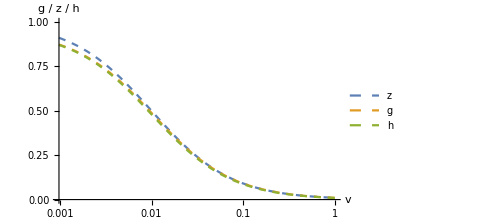

```mathematica
(*plot all three quantities: g, y, h*)
params={β->0.001,u->0.001,n->100};
expressions={ zcalc[n,u,v](*z*) ,gcalc[n,u,v](*g*), hcalc[n,u,v](*h*)}/.params;
LogLinearPlot[expressions,{v,0,1},PlotRange->{0,1},AxesLabel->{"v","g / z / h"},PlotLegends->Placed[{z,g,h},{0.9,0.5}],ImageSize->Medium,PlotStyle->Dashed]
```

```mathematica
(*plot b/c threshold for CD to be favored*)
params={β->0.001,u->0.001,n->40};
expressions={ (zcalc[n,u,v]- hfac hcalc[n,u,v])/(gcalc[n,u,v]-hfac hcalc[n,u,v])}/.params;
LogLinearPlot[expressions,{v,0,1},PlotRange->{0,7},AxesLabel->{"v","critical b/c"},ImageSize->Medium,PlotStyle->Dashed]
```

-Graphics-

### Summary: y, z, g, h

In summary we have

```mathematica
yeval[μ,ν]
zeval[μ,ν]
geval[μ,ν]
heval[μ,ν]
```

(2+μ)/(2+2 μ)

1/(1+ν)

1/2 (1/(1+ν)+1/(1+μ+ν))

(3+μ)/(2 (2+μ) (1+ν))+1/(4 (1+μ+ν))+(-3 μ-μ^2)/(4 (1+μ) (2+μ) (3+μ+ν))

## 3. Using simulation data to check expressions

In this section, we will use the y, z, g, h values taken from simulations to check (qualitatively) the infinite-population expressions we derived above.

```mathematica
simdata=Import["/Users/MariKawakatsu/.julia/dev/CooperationPolarization2/data/calc_data/sim_data_yzgh.csv"];
simdata // MatrixForm (*simdata is using p=0*)
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.98069 | 0.96145 | 0.943574 | 0.943115
0.001 | 0.00223607 | 0.980662 | 0.917702 | 0.901347 | 0.900401
0.001 | 0.005 | 0.980814 | 0.832582 | 0.819153 | 0.81739
0.001 | 0.0111803 | 0.980707 | 0.688565 | 0.6792 | 0.676385
0.001 | 0.025 | 0.980799 | 0.493426 | 0.488553 | 0.485066
0.001 | 0.0559017 | 0.980756 | 0.297027 | 0.295187 | 0.292014
0.001 | 0.125 | 0.980697 | 0.148972 | 0.148456 | 0.146351
0.001 | 0.279508 | 0.980766 | 0.0605266 | 0.0604288 | 0.0594181
0.001 | 0.625 | 0.98076 | 0.0147679 | 0.0147567 | 0.014487)

```mathematica
vs=simdata[[2;;10,2]];
ys=simdata[[2;;10,3]];
zs=simdata[[2;;10,4]];
gs=simdata[[2;;10,5]];
hs=simdata[[2;;10,6]];
```

```mathematica
(*for convenience, define functions for plotting*)xCCbracket4[nn_,bb_,cc_,yy_,zz_,gg_,hh_]:=xCCbracket3/.{n->nn,b->bb,c->cc,y->yy,z->zz,g->gg,h->hh}
xCDbracket4[nn_,bb_,cc_,yy_,zz_,gg_,hh_]:=xCDbracket3/.{n->nn,b->bb,c->cc,y->yy,z->zz,g->gg,h->hh}
xDCbracket4[nn_,bb_,cc_,yy_,zz_,gg_,hh_]:=xDCbracket3/.{n->nn,b->bb,c->cc,y->yy,z->zz,g->gg,h->hh}
xDDbracket4[nn_,bb_,cc_,yy_,zz_,gg_,hh_]:=xDDbracket3/.{n->nn,b->bb,c->cc,y->yy,z->zz,g->gg,h->hh}
```

Finally, we plot the strategy predictions as predicted by our theoretical expressions and simulation data:

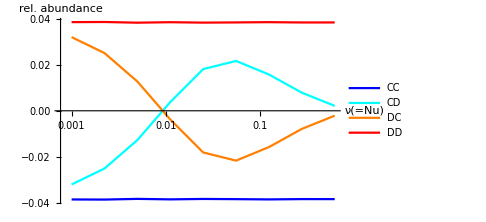

```mathematica
betatemp=0.001; ntemp=40;utemp=0.001;
{dataCC,dataCD,dataDC,dataDD}=Transpose@ Table[{
{vs[[i]],(ntemp(1-utemp))/utemp betatemp/ntemp xCCbracket4[ntemp,1,0.2,ys[[i]],zs[[i]],gs[[i]],hs[[i]]]},
{vs[[i]],(ntemp(1-utemp))/utemp betatemp/ntemp xCDbracket4[ntemp,1,0.2,ys[[i]],zs[[i]],gs[[i]],hs[[i]]]},
{vs[[i]],(ntemp(1-utemp))/utemp betatemp/ntemp xDCbracket4[ntemp,1,0.2,ys[[i]],zs[[i]],gs[[i]],hs[[i]]]},
{vs[[i]],(ntemp(1-utemp))/utemp betatemp/ntemp xDDbracket4[ntemp,1,0.2,ys[[i]],zs[[i]],gs[[i]],hs[[i]]]}},{i,1,9}];
ListLogLinearPlot[{dataCC,dataCD,dataDC,dataDD},
AxesLabel->{"ν(=Nu)","rel. abundance"},PlotLegends->{"CC","CD","DC","DD"},
ImageSize->Medium,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red},Joined->True]
```

```mathematica
(*corresponding theoretical data*)
(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2}];

(*compute y,z,g,h for each v*)
calcdata=Flatten[
Table[{u/.params,v,
ycalc[n,u,v]/.params,zcalc[n,u,v]/.params,gcalc[n,u,v]/.params,hcalc[n,u,v]/.params},
{v,vs}],
0]; (*flatten into a data table*)
headers={"u","v","y","z","g","h"};
calcdata=Prepend[calcdata,headers];
calcdata // MatrixForm
```

(u | v | y | z | g | h
0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.94327
0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.900695
0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.818105
0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.678841
0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.491551
0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.303843
0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.163792
0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0806223
0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0377472)

```mathematica
vs=calcdata[[2;;10,2]];
ys=calcdata[[2;;10,3]];
zs=calcdata[[2;;10,4]];
gs=calcdata[[2;;10,5]];
hs=calcdata[[2;;10,6]];
```

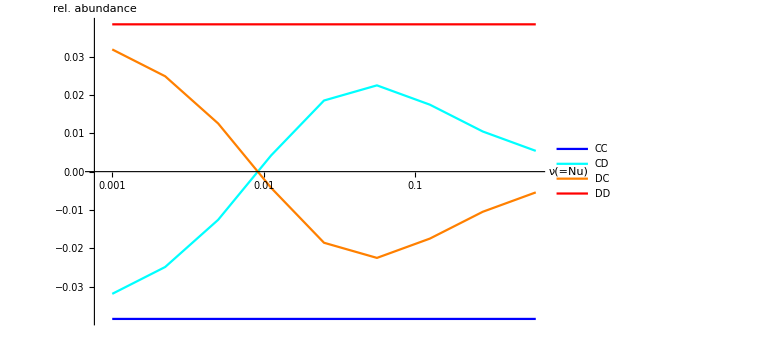

```mathematica
betatemp=0.001; ntemp=40;utemp=0.001;
{dataCC,dataCD,dataDC,dataDD}=Transpose@ Table[{
{vs[[i]],(ntemp(1-utemp))/utemp betatemp/ntemp xCCbracket4[ntemp,1,0.2,ys[[i]],zs[[i]],gs[[i]],hs[[i]]]},
{vs[[i]],(ntemp(1-utemp))/utemp betatemp/ntemp xCDbracket4[ntemp,1,0.2,ys[[i]],zs[[i]],gs[[i]],hs[[i]]]},
{vs[[i]],(ntemp(1-utemp))/utemp betatemp/ntemp xDCbracket4[ntemp,1,0.2,ys[[i]],zs[[i]],gs[[i]],hs[[i]]]},
{vs[[i]],(ntemp(1-utemp))/utemp betatemp/ntemp xDDbracket4[ntemp,1,0.2,ys[[i]],zs[[i]],gs[[i]],hs[[i]]]}},{i,1,9}];
ListLogLinearPlot[{dataCC,dataCD,dataDC,dataDD},
AxesLabel->{"ν(=Nu)","rel. abundance"},PlotLegends->{"CC","CD","DC","DD"},
ImageSize->Large,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red},Joined->True]
```

```mathematica
( calcdata-simdata )/simdata*100//MatrixForm (*percentage error*)
```

(0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0.00803854 | 0.00921494 | 0.0167832 | 0.0164047
0. | -1.93948×10^-14 | 0.0108867 | 0.0216502 | 0.0332394 | 0.0327268
0. | -1.73472×10^-14 | -0.00458474 | 0.0902441 | 0.0902141 | 0.0875389
0. | 4.18928×10^-13 | 0.00630464 | 0.351144 | 0.366694 | 0.363106
0. | -2.77556×10^-14 | -0.00308069 | 1.33228 | 1.33966 | 1.33697
0. | -1.36539×10^-13 | 0.0013051 | 4.03671 | 4.04597 | 4.05096
0. | -4.44089×10^-14 | 0.00731531 | 11.8779 | 11.895 | 11.9166
0. | -1.58882×10^-13 | 0.000285373 | 35.6419 | 35.6392 | 35.6863
0. | -5.32907×10^-14 | 0.000982619 | 160.44 | 160.437 | 160.56)

## 4. Computing strategy frequencies

### Computing the full bracketed terms

We define the following functions to compute the original bracketed terms in (1):

```mathematica
Clear[nn,ββ,pp,bb,cc,μ,μμ,ν,νν];
ΔxCC[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=(1-pp/2)(ββ/nn)xCCbracket3/.{n->nn,b->bb,c->cc,y->yeval[μ,ν]};
ΔxCD[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=(1-pp/2)(ββ/nn)xCDbracket3/.{n->nn,b->bb,c->cc,z->zeval[μ,ν],g-> geval[μ,ν],h-> heval[μ,ν]};
ΔxDC[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=(1-pp/2)(ββ/nn)xDCbracket3/.{n->nn,b->bb,c->cc,z->zeval[μ,ν],g-> geval[μ,ν],h->heval[μ,ν]};
ΔxDD[nn_,bb_,cc_,ββ_,pp_,μ_,ν_]:=(1-pp/2)(ββ/nn)xDDbracket3/.{n->nn,b->bb,c->cc,y-> yeval[μ,ν]};
```

```mathematica
Clear[nn,bb,cc,ββ,pp,μμ,ν];
ΔxCD[nn,bb,cc,ββ,pp,μμ,ν]
```

1/4 (1-pp/2) ββ (cc (-1/(1+ν)+(3+μμ)/(2 (2+μμ) (1+ν))+1/(4 (1+μμ+ν))+(-3 μμ-μμ^2)/(4 (1+μμ) (2+μμ) (3+μμ+ν)))+bb (-(3+μμ)/(2 (2+μμ) (1+ν))-1/(4 (1+μμ+ν))-(-3 μμ-μμ^2)/(4 (1+μμ) (2+μμ) (3+μμ+ν))+1/2 (1/(1+ν)+1/(1+μμ+ν))))

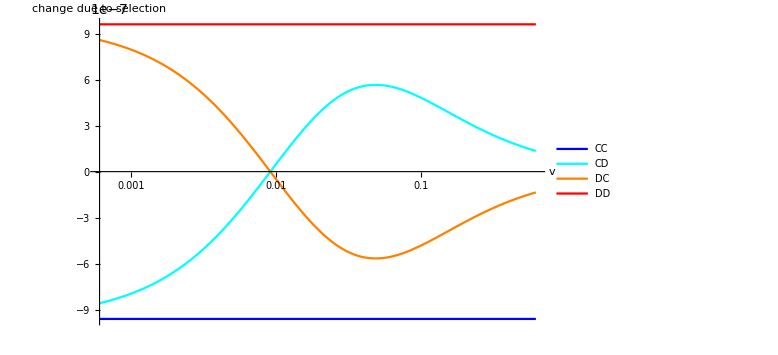

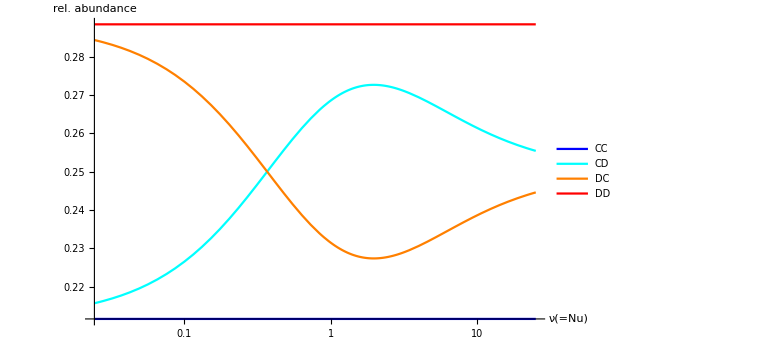

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;
μμ=nn*uu;

plot1=LogLinearPlot[{
ΔxCC[nn,bb,cc,ββ,pp,μμ,nn*vv],
ΔxCD[nn,bb,cc,ββ,pp,μμ,nn*vv],
ΔxDC[nn,bb,cc,ββ,pp,μμ,nn*vv],
ΔxDD[nn,bb,cc,ββ,pp,μμ,nn*vv]},{vv,0,0.625},
AxesLabel->{"v","change due to selection"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},
ImageSize->Large,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red}];

plot2=LogLinearPlot[{
1/4+(nn(1-uu))/uu ΔxCC[nn,bb,cc,ββ,pp,μμ,ν],
1/4+(nn(1-uu))/uu ΔxCD[nn,bb,cc,ββ,pp,μμ,ν],
1/4+(nn(1-uu))/uu ΔxDC[nn,bb,cc,ββ,pp,μμ,ν],
1/4+(nn(1-uu))/uu ΔxDD[nn,bb,cc,ββ,pp,μμ,ν]},{ν,0,0.625*nn},
AxesLabel->{"ν(=Nu)","rel. abundance"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625*nn},Automatic},
ImageSize->Large,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red}];
plot1
plot2
```